```mathematica
compOnlyEdges = Flatten@Map[Thread,Table[Map[Thread,articles[[i]]-> Intersection[Keys[compData],compData[[i]][["LinksList"]]]],{i,1,100}]];
```

```mathematica
CommunityGraphPlot[compOnlyEdges,VertexLabels->Placed[Automatic,Tooltip],Method->"Hierarchical"]
```

-Graphics-

```mathematica
compOnlySingle =Union@Flatten@Append[compOnlyEdges,Table[Keys[compData][[i]]->Keys[compData][[i]],{i,Length[Keys[compData]]}]];
```

```mathematica
CommunityGraphPlot[compOnlySingle,VertexLabels->Placed[Automatic,Tooltip],Method->"Hierarchical"]
```

-Graphics-

```mathematica
CommunityGraphPlot[compOnlyEdges,FindGraphCommunities[compOnlyEdges,Method->#],VertexLabels->Placed[Automatic,Tooltip]]&/@{"Modularity","Centrality","CliquePercolation","Hierarchical","Spectral","VertexMoving"}//Column;
```

```mathematica
groups=Association[
	Flatten[
		Map[
			Thread,
			Thread[
				FindGraphCommunities[compOnlyEdges]->
				{
					"Computational Chemistry Group",
					"Computational Informatics and Data Group",
					"Computational Biology Group",
					"Computational Linguistics Group",
					"Computational -ology and Economics Group",
					"Computational Physics Group",
					"Computational Math Group",
					"Computational Photography Group"
				}
			]
		]
	]
];
```

```mathematica
groupsEdges=Table[Replace[compOnlyEdges[[i]],compOnlyEdges[[i]]-> (groups[compOnlyEdges[[i]][[1]]]-> groups[compOnlyEdges[[i]][[2]]])],{i,Length[compOnlyEdges]}];
```

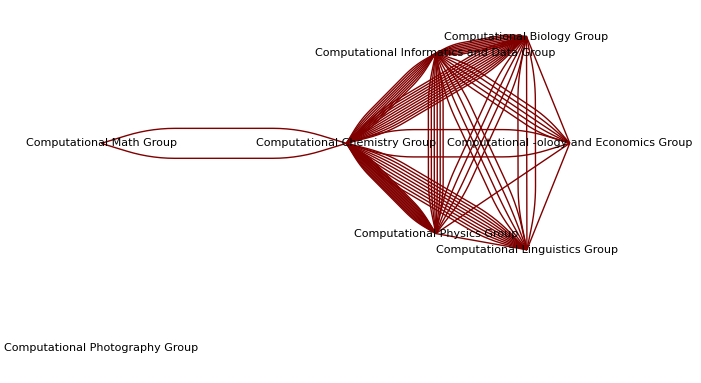

```mathematica
GraphPlot[groupsEdges,SelfLoopStyle->None,VertexLabeling->True]
```

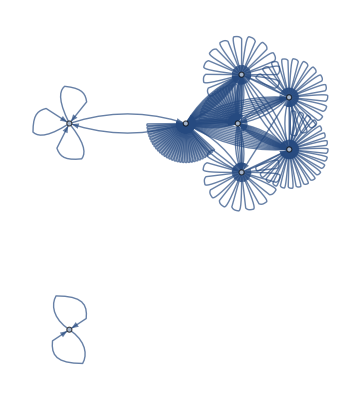

```mathematica
Graph[groupsEdges,VertexLabels->Placed[Automatic,Tooltip]]
```

```mathematica
CommunityGraphPlot[groupsEdges]
```

-Graphics-

```mathematica
noLinks = Complement[Keys[compData],Flatten@FindGraphCommunities[compOnlyEdges]];
```